```mathematica
BlockToSet[b_]:=Block[{result={},pos},
result=Table[
FromDigits[c],
{c,Characters[b]}];
result
]
```

```mathematica
BlockToSet["123"]
```

{1,2,3}

```mathematica
StringToPartition[s_]:=Block[{result={}, blocks=StringSplit[s,"x"]},
result=Table[
BlockToSet[b]
,{b,blocks}
];
result
]
```

```mathematica
StringToPartition["123x4x5"]
```

{{1,2,3},{4},{5}}

```mathematica
PartitionFaculty[p_]:=Fold[Times,Map[Length[#]!&,p]]
```

```mathematica
PartitionFaculty[{{1,2,3},{4},{5}}]
```

6

```mathematica
CompareSymbols[s1_,s2_]:=Block[{str1,str2,c1,c2,p1,p2},
str1=StringDrop[SymbolName[s1],1];
str2=StringDrop[SymbolName[s2],1];
p1=StringToPartition[str1];
p2=StringToPartition[str2];
c1=PartitionFaculty[p1];
c2=PartitionFaculty[p2];
If[c1≠c2,
Less[c1,c2],
str1=StringReplace[str1,"x"->"-"];
str2=StringReplace[str2,"x"->"-"];
AlphabeticOrder[ str1,str2]>0
]
]
```

```mathematica
CompareSymbols[n12x3x4,n123x4]
```

{2,6}

True

```mathematica
CompareSymbols[n123x4,n12x3x4]
```

{6,2}

False

```mathematica
allGraphs4AtomKeysSorted=Sort[allGraphs4AtomKeys,CompareSymbols[allGraphs4[#1,"colofour"],allGraphs4[#2,"colofour"]]&];
```

```mathematica
allNull4Sorted=Sort[allGraphs4NullAtomKeys,CompareSymbols[allGraphs4[#1,"colofourrealnull"],allGraphs4[#2,"colofourrealnull"]]&];
```

```mathematica
With[
{pattern={1,2}},
TableForm[With[{m=MobiusMatrix[allGraphs4]},
Table[If[ HasSubsets[allGraphs4[allNull4Sorted[[i]],"vertexsets"],pattern]&& HasSubsets[allGraphs4[allNull4Sorted[[j]],"vertexsets"],pattern],
Framed[m[[i,j]],FrameStyle->Directive[Red,Thick],Background->LightYellow], 
If[ HasSubsets[allGraphs4[allNull4Sorted[[i]],"vertexsets"],pattern]|| HasSubsets[allGraphs4[allNull4Sorted[[j]],"vertexsets"],pattern],
Framed[m[[i,j]],FrameStyle->Directive[Black,DotDashed],Background->LightYellow], 
Framed[m[[i,j]],FrameStyle->Directive[Black,Dotted]]],
Framed[m[[i,j]],FrameStyle->Directive[Black,Dotted]]]
,{i,1,15},{j,1,15}]
], TableHeadings->{Table[SymbolToLabel[allGraphs4[k,"colofourrealnull"]],{k,allNull4Sorted}], Table[Rotate[SymbolToLabel[allGraphs4[k,"colofourrealnull"]],Pi/2],{k,allNull4Sorted}]},
TableAlignments->{Center, Center}, TableSpacing->{0.2, 0.2}]
]
```

| 1|2|3|4 | 1|2|34 | 1|23|4 | 1|24|3 | 12|3|4 | 13|2|4 | 14|2|3 | 12|34 | 13|24 | 14|23 | 1|234 | 123|4 | 124|3 | 134|2 | 1234
1|2|3|4 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | -6
1|2|34 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 2
1|23|4 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 2
1|24|3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 2
12|3|4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 2
13|2|4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 2
14|2|3 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 2
12|34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
13|24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
14|23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
1|234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
123|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
124|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
134|2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
1234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

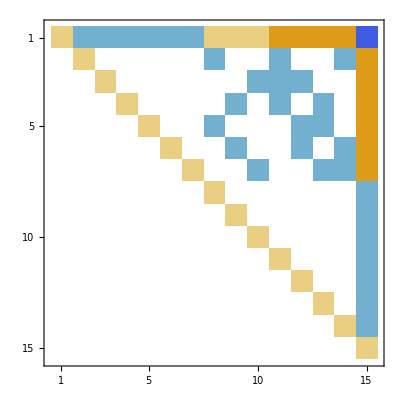

```mathematica
MobiusMatrix[allGraphs4]//MatrixPlot
```

```mathematica
Total[{{0,1,0,0,0,0,0,-1,-1,0,0,0,-1,0,2},{0,0,1,0,0,0,0,-1,0,-1,0,0,0,-1,2},{0,0,0,1,0,0,0,-1,0,0,-1,-1,0,0,2},{0,0,0,0,1,0,0,0,-1,-1,-1,0,0,0,2},{0,0,0,0,0,1,0,0,0,-1,0,-1,-1,0,2},{0,0,0,0,0,0,1,0,0,0,-1,0,-1,-1,2},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}]
```

{0,1,1,1,1,1,1,-2,-1,-2,-2,-1,-2,-1,6}